# Adding species to chemical reaction networks: preserving rank preserves nondegenerate behaviours

Murad Banaji, Balázs Boros, Josef Hofbauer

This Mathematica Notebook is a supplementary material to the paper which has  the same title as this document. It contains some of the calculations appearing in the paper.

## 0 Focal values

Derive  and , the first and the second focal values for the differential equation

Theoretical background: Chapter 4 in Dumortier, Llibre, Artés: Qualitative Theory of Planar Differential Systems.

```mathematica
m = 2;
cd = {}; R2cd = {};
For[k=2, k≤2m+1, k++, For[i=0, i≤k, i++,
    {cd=Join[cd,{Subscript[c, k,i],Subscript[d, k,i]}], R2cd = Join[R2cd,{Subscript[R, k,i]->Subscript[c, k,i]+Subscript[d, k,i] I}]}]];
coeffsxy = CoefficientList[ComplexExpand[Sum[Sum[Subscript[R, k,i] z^(k-i)(z*)^i,{i,0,k}], {k,2,2m+1}]
    /.R2cd/.{z->x+y I}], {x,y}];
cond = True;
For[k=2, k≤2m+1, k++, For[i=0, i≤k, i++,
    {cond = cond && (Subscript[f, i,k-i]==ComplexExpand[Re[coeffsxy[[i+1,k-i+1]]]]) &&
    (Subscript[g, i,k-i]==ComplexExpand[Im[coeffsxy[[i+1,k-i+1]]]])}]];
cd2fg = Solve[cond,cd][[1]];

For[k=2, k≤2m+1, k++, Subscript[R, k]=Sum[Subscript[R, k,i] z^(k-i)w^i,{i,0,k}]];

(* F[i,j] computes the polynomial Subscript[F, i](Subscript[h, j]) *)
F[i_,j_] := Module[{coeffs,M,mtx},
coeffs = CoefficientList[D[Subscript[R, i] Subscript[h, j],{z,1}],{z,w}];
M = Dimensions[coeffs][[1]]-1;
mtx = (coeffs + Transpose[coeffs*]) Table[If[k+l==M&&k≠l,1/(k-l),0],{k,0,M},{l,0,M}];
I (z^Range[0,M]).mtx.w^Range[0,M]];

Subscript[h, 0] = 1;
For[k=1, k≤2m-1, k++, Subscript[h, k] = Sum[F[k+1-l,l],{l,0,k-1}]];

(* H[k,j] computes Subscript[H, k](Subscript[h, j]), note that one of k and j is even, the other one is odd in all of the interesting cases *)
H[k_,j_] := Module[{},
coeffs = CoefficientList[Subscript[h, j],{z,w}];
Sum[Coefficient[Subscript[R, k],z^a w^(k-a)]coeffs[[((k-2a+1)+j)/2+1,(j-(k-2a+1))/2+1]],{a,(k+1-j)/2,(k+1+j)/2}]];
For[j=1,j≤m,j++,Subscript[L, j]=Simplify[ComplexExpand[2π Re[Sum[H[2j+1-l,l],{l,0,2j-1}]]/.R2cd/.cd2fg]]];
```

Display the first focal value, . The second focal value, , is somewhat longer. Important note:  and  include the division by , so they are the Taylor coefficients (not simply the respective derivatives).

```mathematica
Print[" ",Subscript[L, 1]];
```

1/4 π (f_(1,2)+f_(1,1) f_(2,0)+3 f_(3,0)+f_(0,2) (f_(1,1)+2 g_(0,2))+3 g_(0,3)-g_(0,2) g_(1,1)-2 f_(2,0) g_(2,0)-g_(1,1) g_(2,0)+g_(2,1))

Good practice: compute the focal values once, and save them in a file. When needed, load from that file.

```mathematica
L1 = Subscript[L, 1]; L2 = Subscript[L, 2]; (* when storing in a file, better avoiding subscripts *)
path="C://bboros/Dropbox/murad/lifting/tex/computations/focal_values.mx";
DumpSave[path,{L1,L2}];
Protect[path];
Off[Remove::rmptc];
Remove["Global`*"]; (* clear all variables *)
On[Remove::rmptc];
Unprotect[path];
```

Define a module that computes the necessary partial derivatives. To be used later.

```mathematica
GetDerivatives[fg_,equilibrium_,m_]:=Module[{J,xyshift,T,Tinvuv,FG,derivatives},
J=Simplify[D[fg,{{x,y}}]/.equilibrium];
xyshift = {x->x+(x/.equilibrium), y->y+(y/.equilibrium)};
T = {{1,0},{-a/ω,-b/ω}};
Tinvuv = Inverse[T].{u,v};
FG = (T . fg/.xyshift)/ω /.{x->Tinvuv[[1]],y->Tinvuv[[2]]}/.{a->J[[1,1]],b-> J[[1,2]]};
derivatives={};
For[i=0, i≤2m+1, i++, For[j=0, j≤2m+1-i, j++, 
derivatives = Join[derivatives, Simplify[{Subscript[f, i,j]->(D[FG[[1]],{u,i},{v,j}]/((i!)*( j!))/.{u->0,v->0}), Subscript[g, i,j]->(D[FG[[2]],{u,i},{v,j}]/((i!)*( j!))/.{u->0,v->0})}]]]];
derivatives];
```

## 4.1 Schlögl model

On any compact subinterval of , the vectorfield  converges uniformly to  as .

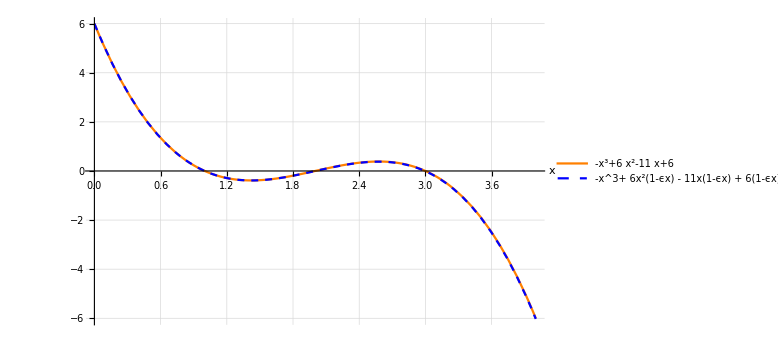

```mathematica
eps=10^-4;
feps=-x^3+6 x^2(1-ϵ x)-11x(1-ϵ x)+6(1-ϵ x)^2;
Plot[{feps/.{ϵ->0},feps/.{ϵ->eps}},{x,0,4},PlotStyle->{Orange,{Dashed,Blue}},PlotRange->All,PlotLegends->Placed[{feps/.{ϵ->0},"-x^3+ 6x^2(1-ϵx) - 11x(1-ϵx) + 6(1-ϵx)^2 with ϵ = " <>ToString[TraditionalForm[eps]]},{0.55,0.8}],LabelStyle->Directive[FontSize->16],AxesLabel->{x,},GridLines->Automatic,ImageSize->Large]
```

## 4.2 Lotka-Volterra Autocatalator (LVA)

Find the positive equilibrium of the LVA with one reversible reaction (when it exists).

```mathematica
fg=Subscript[κ, 1] x^2{1,0}+Subscript[κ, 2] x^3{-1,0}+Subscript[κ, 3] x y{-1,1}+Subscript[κ, 4] y{0,-1};
κpositive=Subscript[κ, 1]>0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 4]>0;
xypositive=x>0&&y>0;
Print["positive equilibrium: ",Simplify[Reduce[fg==0&&κpositive&&xypositive]]];
```

positive equilibrium: κ_1>0&&κ_2>0&&κ_3>0&&0<κ_4<(κ_1 κ_3)/κ_2&&y==(κ_4 (κ_1 κ_3-κ_2 κ_4))/κ_3^3&&x==κ_4/κ_3

Check the sign of the determinant and the trace of the Jacobian matrix at the positive equilibrium. The determinant is always positive, while the trace changes sign at .

```mathematica
equilibrium={x->Subscript[κ, 4]/Subscript[κ, 3],y->(Subscript[κ, 4] (Subscript[κ, 1] Subscript[κ, 3]-Subscript[κ, 2] Subscript[κ, 4]))/Subscript[κ, 3]^3};
J=D[fg,{{x,y}}]/.equilibrium;
Print[" ",Simplify[Det[J]]];
omegasubst = Simplify[{ω->√Det[J]},κpositive];
Print[" ",Simplify[Tr[J]]];
```

(κ_4^2 (κ_1 κ_3-κ_2 κ_4))/κ_3^2

(κ_4 (κ_1 κ_3-2 κ_2 κ_4))/κ_3^2

When the trace vanishes, compute the first focal value. It is negative, the Andronov-Hopf bifurcation is supercritical.

```mathematica
tracevanish={Subscript[κ, 4]->(Subscript[κ, 1] Subscript[κ, 3])/(2 Subscript[κ, 2])};
derivatives=GetDerivatives[fg,equilibrium,1];
derivativessimp=Simplify[derivatives/.omegasubst/.tracevanish,κpositive];
Get[path];
Print[" ",Simplify[L1/.derivativessimp,κpositive]];
```

-(√2 π κ_2^2)/(√(κ_1^3 κ_3))

Now homogenise the LVA and find the curve of positive equilibria.

```mathematica
fgh=Subscript[κ, 1] x^2 z{1,0,-1}+Subscript[κ, 2] x^3{-1,0,1}+Subscript[κ, 3] x y{-1,1,0}+Subscript[κ, 4] y{0,-1,1};
κpositive=Subscript[κ, 1]>0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 4]>0;
xyzpositive=x>0&&y>0&&z>0;
Print["positive equilibria: ",Simplify[Reduce[fgh==0&&κpositive&&xyzpositive,{x,y,z}]]];
```

positive equilibria: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&x==κ_4/κ_3&&y>0&&z==(x κ_2+(y κ_3)/x)/κ_1

Parametrise the curve of positive equilibria by . For each positive equilibrium, restrict the dynamics to its positive stoichiometric class and eliminate z. Check the sign of the determinant and the trace of the Jacobian matrix at the positive equilibrium. The determinant is always positive, while the trace changes sign at  .

```mathematica
equilibrium={x->Subscript[κ, 4]/Subscript[κ, 3],y->t,z->Subscript[κ, 4]/Subscript[κ, 3] Subscript[κ, 2]/Subscript[κ, 1]+Subscript[κ, 3]/Subscript[κ, 1] Subscript[κ, 3]/Subscript[κ, 4] t};
fg=fgh[[1;;2]]/.{z->(x+y+z/.equilibrium)-x-y};
J=D[fg,{{x,y}}]/.equilibrium;
Print[" ",Simplify[Det[J]]];
omegasubst = Simplify[{ω->√Det[J]},κpositive];
Print[" ",Simplify[Tr[J]]];
```

(t κ_4 (κ_3^2+κ_1 κ_4))/κ_3

t κ_3-((κ_1+κ_2) κ_4^2)/κ_3^2

When the trace vanishes, compute the first focal value. It is negative, the Andronov-Hopf bifurcation is supercritical.

```mathematica
tracevanish={t->((Subscript[κ, 1]+Subscript[κ, 2]) Subscript[κ, 4]^2)/Subscript[κ, 3]^3};
derivatives=GetDerivatives[fg,equilibrium,1];
derivativessimp=Simplify[derivatives/.omegasubst/.tracevanish,κpositive];
Get[path];
Print[" ",Simplify[L1/.derivativessimp,κpositive]];
```

-(π √(κ_1+κ_2) κ_3^2 (2 κ_3^2+κ_1 κ_4))/(4 (κ_4 (κ_3^2+κ_1 κ_4))^(3/2))

## 4.3 Lotka reactions

The ODE of the homogenised Lotka reactions has negative divergence on the positive orthant . Thus, there is no periodic solution.

```mathematica
fgh=Subscript[κ, 1] x z{1,0,-1}+Subscript[κ, 2] x y{-1,1,0}+Subscript[κ, 3] y{0,-1,1};
Print["divergence = ",Simplify[Div[fgh/(x y z),{x,y,z}]]];
```

divergence = -κ_3/(x z^2)

The unique positive equilibrium in the positive stoichiometric class  with  is asymptotically stable.

```mathematica
equilibrium={x->Subscript[κ, 3]/Subscript[κ, 2],y->Subscript[κ, 1]/Subscript[κ, 2] t,z->t};
fg=fgh[[1;;2]]/.{z->(x+y+z/.equilibrium)-x-y};
J=D[fg,{{x,y}}]/.equilibrium;
Print[" ",Simplify[Det[J]]];
Print[" ",Simplify[Tr[J]]];
```

(t κ_1 (κ_1+κ_2) κ_3)/κ_2

-(κ_1 κ_3)/κ_2

Since each of the corner equilibria  and  is a saddle (assuming ), the  - limit set of each positive initial condition is disjoint from the boundary. Thus, by the Poincaré-Bendixson Theorem, the system is permanent.

```mathematica
fg=fgh[[1;;2]]/.{z->c-x-y};
J=D[fg,{{x,y}}];
Print["at the corner equilibrium ,  ",Simplify[Det[J]/.{x->c,y->0}]];
Print["at the corner equilibrium ,  ",Simplify[Det[J]/.{x->0,y->0}]];
```

at the corner equilibrium ,  c κ_1 (-c κ_2+κ_3)

at the corner equilibrium ,  -c κ_1 κ_3

## 4.4 Brusselator

We start with verifying for the Brusselator that the Andronov-Hopf bifurcation is supercritical.

```mathematica
fg=Subscript[κ, 1]{1,0}+Subscript[κ, 2] x{-1,0}+Subscript[κ, 3] x{-1,1}+Subscript[κ, 4] x^2 y{1,-1};
κpositive=Subscript[κ, 1]>0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 4]>0;
equilibrium={x->Subscript[κ, 1]/Subscript[κ, 2],y->(Subscript[κ, 2] Subscript[κ, 3])/(Subscript[κ, 1] Subscript[κ, 4])};
J=D[fg,{{x,y}}]/.equilibrium;
Print[" ",Det[J]];
omegasubst = Simplify[{ω->√Det[J]},κpositive];
Print[" ",Tr[J]];
```

(κ_1^2 κ_4)/κ_2

-κ_2+κ_3-(κ_1^2 κ_4)/κ_2^2

```mathematica
tracevanish={Subscript[κ, 3]->Subscript[κ, 2]+(Subscript[κ, 1]^2 Subscript[κ, 4])/Subscript[κ, 2]^2};
derivatives=GetDerivatives[fg,equilibrium,1];
derivativessimp=Simplify[derivatives/.omegasubst/.tracevanish,κpositive];
Get[path];
Print[" ",Simplify[L1/.derivativessimp,κpositive]];
```

-(π (2 κ_2^4+κ_1^2 κ_2 κ_4))/(4 κ_1^3 √(κ_2 κ_4))

Homogenise the Brusselator and observe first that  is an equilibrium on the boundary for every .
Since the two eigenvalues within the triangle  are negative reals,
the corner equilibrium  is asymptotically stable relative to its positive stoichiometric class.
Therefore, the homogenised Brusselator is not permanent.

```mathematica
fgh=Subscript[κ, 1] z{1,0,-1}+Subscript[κ, 2] x{-1,0,1}+Subscript[κ, 3] x{-1,1,0}+Subscript[κ, 4] x^2 y{1,-1,0};
eigs=Eigenvalues[D[fgh,{{x,y,z}}]/.{x->0,z->0}];
Print["eigenvalues: ",eigs];
Print["two negative real eigenvalues for ",Reduce[eigs[[2]]<0&&eigs[[3]]<0&&κpositive]];
```

eigenvalues: {0,1/2 (-κ_1-κ_2-κ_3-√(-4 κ_1 κ_3+(κ_1+κ_2+κ_3)^2)),1/2 (-κ_1-κ_2-κ_3+√(-4 κ_1 κ_3+(κ_1+κ_2+κ_3)^2))}

two negative real eigenvalues for κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0

Let us now turn to the positive equilibria of the homogenised Brusselator.

```mathematica
xyzpositive=x>0&&y>0&&z>0;
Print["positive equilibria: ",Simplify[Reduce[fgh==0&&κpositive&&xyzpositive,{x,y,z}]]];
```

positive equilibria: κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&x>0&&y==κ_3/(x κ_4)&&z==(x (κ_2+κ_3-x y κ_4))/κ_1

```mathematica
equilibrium={x->t,y->Subscript[κ, 3]/Subscript[κ, 4] 1/t,z->Subscript[κ, 2]/Subscript[κ, 1] t};
```

Eliminate  using , where . Then compute the Jacobian matrix at the positive equilibrium, as well as its trace and determinant.

```mathematica
fg=fgh[[1;;2]]/.{z->(x+y+z/.equilibrium)-x-y};
J=D[fg,{{x,y}}]/.equilibrium;
detJ=Det[J];
trJ=Tr[J];
Print[" ",MatrixForm[J]];
Print[" ",detJ];
Print[" ",trJ];
```

(-κ_1-κ_2+κ_3 | -κ_1+t^2 κ_4
-κ_3 | -t^2 κ_4)

-κ_1 κ_3+t^2 κ_1 κ_4+t^2 κ_2 κ_4

-κ_1-κ_2+κ_3-t^2 κ_4

For the fold bifurcation of the positive equilibrium, find where the determinant is zero and the trace is nonzero .

```mathematica
Print[" and  : ", Simplify[Reduce[detJ==0&&trJ!=0&&t>0&&κpositive&&(x+y+z/.equilibrium)==c&&c>0,{t,Subscript[κ, 4]}]]];
```

and  : t==(c κ_1)/(2 (κ_1+κ_2))&&κ_4==(κ_1 κ_3)/(t^2 (κ_1+κ_2))&&(0<κ_3<(κ_1+κ_2)^2/κ_2||κ_3>(κ_1+κ_2)^2/κ_2)&&c>0&&κ_1>0&&κ_2>0

To check the transversality condition for the fold bifurcation, the verify the regularity of the map , here  can be any of .

```mathematica
fold={t->(c Subscript[κ, 1])/(2 (Subscript[κ, 1]+Subscript[κ, 2])),Subscript[κ, 4]->(4(Subscript[κ, 1]+Subscript[κ, 2])Subscript[κ, 3])/(c^2 Subscript[κ, 1])};
fgc=fgh[[1;;2]]/.{z->c-x-y};
map=Join[fgc,{Det[D[fgc,{{x,y}}]]}];
For[i=1,i<=4,i++,{Print["determinant of the R^3 to R^3 map when differentiated w.r.t. ",Subscript[κ, i],": ",Simplify[Det[D[map,{{x,y,Subscript[κ, i]}}]/.equilibrium/.fold]]]}];
```

determinant of the R^3 to R^3 map when differentiated w.r.t. κ_1: (2 κ_1 κ_2 κ_3^2)/(κ_1+κ_2)

determinant of the R^3 to R^3 map when differentiated w.r.t. κ_2: -(2 κ_1^2 κ_3^2)/(κ_1+κ_2)

determinant of the R^3 to R^3 map when differentiated w.r.t. κ_3: -2 κ_1^2 κ_3

determinant of the R^3 to R^3 map when differentiated w.r.t. κ_4: (c^2 κ_1^3 κ_3)/(2 (κ_1+κ_2))

For the Andronov-Hopf bifurcation, find where the determinant is positive and the trace is zero (Routh-Hurwitz).

```mathematica
Print[" and  : ",Reduce[detJ>0&&trJ==0&&t>0&&κpositive,Subscript[κ, 4]]];
```

and  : κ_1>0&&κ_2>0&&κ_3>(κ_1^2+2 κ_1 κ_2+κ_2^2)/κ_2&&t>0&&κ_4==-(κ_1+κ_2-κ_3)/t^2

Compute the first focal value .

```mathematica
tracevanish={Subscript[κ, 4]->(Subscript[κ, 3]-Subscript[κ, 1]-Subscript[κ, 2])/t^2};
omegasubst = Simplify[{ω->√Det[J]}];
derivatives=GetDerivatives[fg,equilibrium,2];
derivativessimp=Simplify[derivatives/.omegasubst/.tracevanish,κpositive];
Get[path];
κ2ab={Subscript[κ, 2]->a Subscript[κ, 1],Subscript[κ, 3]->b Subscript[κ, 1]};
Print[" ",Simplify[L1/.derivativessimp/.κ2ab,Subscript[κ, 1]>0]];
```

((4+a^4-a^3 (-7+b)-5 b+5 b^2-2 b^3-a^2 (-15+8 b+b^2)+a (13-12 b+3 b^2+b^3)) π)/(4 (-1-a^2+a (-2+b))^(3/2) (2+a-b) t^2)

We now  analyse the enumerator  and the denominator  of  (notice that we multiply both of them by ). The denominator is positive, while the enumerator can have any sign. The Andronov-Hopf bifurcation therefore can be supercritical, subcritical, or degenerate.

```mathematica
Pab=-(4+a^4-a^3 (-7+b)-5 b+5 b^2-2 b^3-a^2 (-15+8 b+b^2)+a (13-12 b+3 b^2+b^3));
Qab=-(-1-a^2+a (-2+b))^(3/2) (2+a-b);
abpositive=a>0&&b>0;
H=Simplify[(Subscript[κ, 3]>(Subscript[κ, 1]+Subscript[κ, 2])^2/Subscript[κ, 2])/.κ2ab,Subscript[κ, 1]>0&&abpositive];
Print["eigenvalues are  : ",Reduce[H&&abpositive]];
Print[" : ",Reduce[Qab>0&&H&&abpositive]];
Print["coeffs of  in  : ",MatrixForm[CoefficientList[Pab,b]]];
Print[" : ",Reduce[Pab==0&&H&&abpositive,b]];
```

eigenvalues are  : a>0&&b>(1+2 a+a^2)/a

: a>0&&b>(1+2 a+a^2)/a

coeffs of  in  : (-4-13 a-15 a^2-7 a^3-a^4
5+12 a+8 a^2+a^3
-5-3 a+a^2
2-a)

: (a==Root1.70Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941&&b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,2])||(Root1.70Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941<a<2&&(b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,2]||b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,3]))||(a==2&&b==6)||(a>2&&b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,3])

We now depict the sign of  as a function of  and .

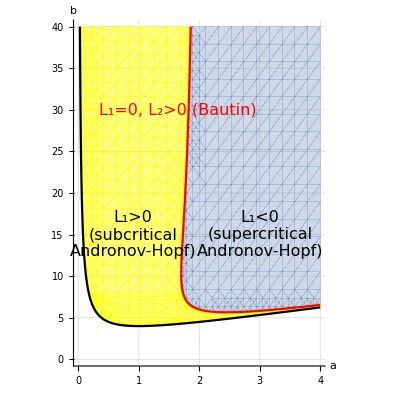

```mathematica
amax=4;
bmax=40;
bmaxsmall=8;
Pneg=RegionPlot[Pab<0&&a>0&&b>(a+1)^2/a,{a,0,amax},{b,0,bmax},GridLines->Automatic,BoundaryStyle->None,AxesLabel->{Style[a,Bold,16],Style[b,Bold,16]},Frame->None,Axes->True];
Ppos1=RegionPlot[Pab>0&&a>0&&b>(a+1)^2/a,{a,0,amax},{b,bmaxsmall,bmax},PlotStyle->{Yellow,Opacity[0.5]},BoundaryStyle->None];
Ppos2=RegionPlot[Pab>0&&a>0&&b>(a+1)^2/a,{a,0,amax},{b,0,bmaxsmall},PlotStyle->{Yellow,Opacity[0.5]},BoundaryStyle->None];
det0=Plot[(a+1)^2/a,{a,0,amax},PlotStyle->Black,PlotRange->{{0,amax},{0,bmax}}];
polynom=4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&;
b2=Root[polynom,2];
b3=Root[polynom,3];
plotb2=Plot[b2,{a,Root"1.70"Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941,2},PlotStyle->Red,PlotRange->{{0,amax},{0,bmax}}];
plotb3a=Plot[b3,{a,Root"1.70"Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941,2},PlotStyle->Red,PlotRange->{{0,amax},{0,bmax}}];
plotb3b=Plot[b3,{a,2,amax},PlotStyle->Red,PlotRange->{{0,amax},{0,bmax}}];
txt=Graphics[{Text[Style["L_1>0\n(subcritical\nAndronov-Hopf)",16],{0.9,15}],Text[Style["L_1<0\n(supercritical\nAndronov-Hopf)",16],{3,15}],Rotate[Text[Style["L_1=0, L_2>0 (Bautin)",16,Red],{1.65,30}],90 Degree]}];
Show[Pneg,Ppos1,Ppos2,det0,plotb2,plotb3a,plotb3b,txt]
```

Compute the second focal value, , where . Turns out it is always positive, justifying the red label on the above figure.
Thus, one can find parameter values for which the equilibrium is repelling and is surrounded by two limit cycles (the inner one is stable, the outer one is unstable).

```mathematica
L2ab=Simplify[L2/.derivativessimp/.κ2ab,Subscript[κ, 1]>0];
Print[" ",L2ab];
Print[" : ",Reduce[L2ab<0&&Pab==0&&H&&abpositive&&t>0]];
Print[" : ",Reduce[L2ab==0&&Pab==0&&H&&abpositive&&t>0]];
Print[" : ",Reduce[L2ab>0&&Pab==0&&H&&abpositive&&t>0,b]];
```

1/(48 (-1-a^2+a (-2+b))^(7/2) (2+a-b)^2 t^4)(684+139 a^9+a^8 (1713-552 b)-1872 b+2845 b^2-2714 b^3+1655 b^4-598 b^5+96 b^6+a^7 (8783-6352 b+718 b^2)+a^6 (25193-28496 b+8960 b^2-89 b^3)+a^5 (45129-68392 b+36601 b^2-5978 b^3-649 b^4)+a^4 (52759-98200 b+73973 b^2-25270 b^3+2085 b^4+662 b^5)+a^3 (40453-87392 b+83988 b^2-43637 b^3+11483 b^4-680 b^5-272 b^6)+a (5528-14376 b+19285 b^2-16108 b^3+8707 b^4-3039 b^5+677 b^6-86 b^7)+a^2 (19683-47392 b+54814 b^2-37650 b^3+15806 b^4-3778 b^5+338 b^6+43 b^7)) π

: False

: False

: t>0&&((a==Root1.70Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941&&b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,2])||(Root1.70Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941<a<2&&(b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,2]||b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,3]))||(a==2&&b==6)||(a>2&&b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,3]))

We now verify the nondegeneracy of the Bautin bifurcation (Section 8.3 in Kuznetsov: Elements of Applied Bifurcation Theory). The approach we follow here is that  are fixed, and  serve as bifurcation parameters. To check that the map  is regular at the critical value, we need a more general formula of the first focal value, not assuming that the real part of the eigenvalues is zero (but still assuming the Jacobian matrix at the equilibrium is of the form (μ | -ω
ω | μ)). Derivation of this more general first focal value formula can be carried out following http://www.scholarpedia.org/article/Bautin_bifurcation. Important note: below  and  are the partial derivatives, i.e.,  and . We remark that the formula derived below is valid only for .

```mathematica
n=2;
A={{μ,-ω},{ω,μ}};
B[x_,y_]:=Sum[{Subscript[F, Count[{k,l},1],Count[{k,l},2]],Subscript[G, Count[{k,l},1],Count[{k,l},2]]}x[[k]]y[[l]],{k,1,n},{l,1,n}];
CC[x_,y_,z_]:=Sum[{Subscript[F, Count[{k,l,m},1],Count[{k,l,m},2]],Subscript[G, Count[{k,l,m},1],Count[{k,l,m},2]]}x[[k]]y[[l]]z[[m]],{k,1,n},{l,1,n},{m,1,n}];
q={-1/(√2),ⅈ/(√2)};
p=q;
Q1=Simplify[CC[q,q,q*]];
Q2=Simplify[B[q,1/Det[A] A.B[q,q*]]];
Q3=Simplify[B[q*,Inverse[2(μ+I ω) IdentityMatrix[2]-A].B[q,q]]];
Subscript[c, 1]=Simplify[p*.Simplify[1/2 Q1+Q2+1/2 Q3]];
L1general=Simplify[1/ω ComplexExpand[Re[Subscript[c, 1]]]-μ/ω^2 ComplexExpand[Im[Subscript[c, 1]]]];
Print[" ",L1general];
```

1/(8 ω^2 (μ^2+ω^2) (μ^2+9 ω^2))((3 μ^3 ω+11 μ ω^3) F_(0,2)^2+(μ^5+10 μ^3 ω^2+9 μ ω^4) F_(0,3)+8 μ^3 ω F_(1,1)^2+8 μ ω^3 F_(1,1)^2+μ^4 ω F_(1,2)+10 μ^2 ω^3 F_(1,2)+9 ω^5 F_(1,2)+3 μ^4 F_(1,1) F_(2,0)+28 μ^2 ω^2 F_(1,1) F_(2,0)+9 ω^4 F_(1,1) F_(2,0)+5 μ^3 ω F_(2,0)^2+29 μ ω^3 F_(2,0)^2+μ^5 F_(2,1)+10 μ^3 ω^2 F_(2,1)+9 μ ω^4 F_(2,1)+μ^4 ω F_(3,0)+10 μ^2 ω^3 F_(3,0)+9 ω^5 F_(3,0)-6 μ^3 ω F_(1,1) G_(0,2)+10 μ ω^3 F_(1,1) G_(0,2)+5 μ^3 ω G_(0,2)^2+29 μ ω^3 G_(0,2)^2+μ^4 ω G_(0,3)+10 μ^2 ω^3 G_(0,3)+9 ω^5 G_(0,3)-6 μ^3 ω F_(2,0) G_(1,1)+10 μ ω^3 F_(2,0) G_(1,1)-3 μ^4 G_(0,2) G_(1,1)-28 μ^2 ω^2 G_(0,2) G_(1,1)-9 ω^4 G_(0,2) G_(1,1)+8 μ^3 ω G_(1,1)^2+8 μ ω^3 G_(1,1)^2+F_(0,2) ((3 μ^4+28 μ^2 ω^2+9 ω^4) F_(1,1)+32 μ ω^3 F_(2,0)+3 μ^4 G_(0,2)+28 μ^2 ω^2 G_(0,2)+9 ω^4 G_(0,2)+10 μ^3 ω G_(1,1)+26 μ ω^3 G_(1,1))-μ^5 G_(1,2)-10 μ^3 ω^2 G_(1,2)-9 μ ω^4 G_(1,2)+10 μ^3 ω F_(1,1) G_(2,0)+26 μ ω^3 F_(1,1) G_(2,0)-3 μ^4 F_(2,0) G_(2,0)-28 μ^2 ω^2 F_(2,0) G_(2,0)-9 ω^4 F_(2,0) G_(2,0)+32 μ ω^3 G_(0,2) G_(2,0)-3 μ^4 G_(1,1) G_(2,0)-28 μ^2 ω^2 G_(1,1) G_(2,0)-9 ω^4 G_(1,1) G_(2,0)+3 μ^3 ω G_(2,0)^2+11 μ ω^3 G_(2,0)^2+μ^4 ω G_(2,1)+10 μ^2 ω^3 G_(2,1)+9 ω^5 G_(2,1)-μ^5 G_(3,0)-10 μ^3 ω^2 G_(3,0)-9 μ ω^4 G_(3,0))

Now that we have the general formula for , let us apply it to the lifted Brusselator. After that, we compute the relevant determinant for checking the transversality condition of the Bautin bifurcation.

```mathematica
xyshift = {x->x+(x/.equilibrium), y->y+(y/.equilibrium)};
T = {{ω,0},{(d-a)/2,-b}};
Tinvuv = Inverse[T].{u,v};
FG = T . fg/.xyshift /.{x->Tinvuv[[1]],y->Tinvuv[[2]]}/.{a->J[[1,1]],b-> J[[1,2]],d->J[[2,2]]};
m=1;
derivatives={};
For[i=0, i≤2m+1, i++, For[j=0, j≤2m+1-i, j++, 
derivatives = Join[derivatives, Simplify[{Subscript[F, i,j]->(D[FG[[1]],{u,i},{v,j}]/.{u->0,v->0}), Subscript[G, i,j]->(D[FG[[2]],{u,i},{v,j}]/.{u->0,v->0})}]]]];
musubst=Simplify[{μ->Tr[J]/2}];
omegasubst = Simplify[{ω->(√(4Det[J]-Tr[J]^2))/2}];
L1gen=Simplify[L1general/.Simplify[derivatives]/.musubst/.omegasubst];
det=Simplify[Det[Simplify[D[{Tr[J],L1gen},{{Subscript[κ, 3],Subscript[κ, 4]}}]/.tracevanish]/.κ2ab],Subscript[κ, 1]>0];
Print["determinant of the R^3 to R^3 map: ",det];
Print[" : ",Reduce[det>0&&Pab==0&&H&&abpositive&&Subscript[κ, 1]>0,b]];
Print[" : ",Reduce[det==0&&Pab==0&&H&&abpositive&&Subscript[κ, 1]>0,b]];
Print[" : ",Reduce[det<0&&Pab==0&&H&&abpositive&&Subscript[κ, 1]>0,b]];
```

determinant of the R^3 to R^3 map: -(-12+5 a^6+a^5 (39-14 b)+40 b-34 b^2+8 b^3+a^4 (107-83 b+12 b^2)+a^3 (125-141 b+51 b^2-2 b^3)-a^2 (-48+46 b-33 b^2+9 b^3+b^4)+a (-16+66 b-39 b^2+b^3+2 b^4))/(8 (-1-a^2+a (-2+b))^(7/2) (2+a-b)^2 κ_1^3)

: κ_1>0&&Root1.70Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941<a<2&&b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,3]

: κ_1>0&&a==Root1.70Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941&&b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,2]

: κ_1>0&&((Root1.70Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941<a≤2&&b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,2])||(a>2&&b==Root[4+13 a+15 a^2+7 a^3+a^4+(-5-12 a-8 a^2-a^3) #1+(5+3 a-a^2) #1^2+(-2+a) #1^3&,3]))

By the above, the transversality condition is fulfilled except when Root"1.70"Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941. Below we find the symbolic value of Root"1.70"Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941.

```mathematica
Simplify[Root"1.70"Root[-503-848 #1-104 #1^2+320 #1^3+80 #1^4&,4]1.7015342436087941]
```

1/10 (-10+√(5 (73+22 √11)))

We now turn to the Bogdanov-Takens bifurcation (http://www.scholarpedia.org/article/Bogdanov-Takens_bifurcation or Section 8.4 in Kuznetsov: Elements of Applied Bifurcation Theory). Let us start with finding the parameter values, where  and .

```mathematica
Print[" and  : ",Simplify[Reduce[detJ==0&&trJ==0&&c==Simplify[(x+y+z/.equilibrium)]&&κpositive&&t>0&&c>0,{t,Subscript[κ, 3],Subscript[κ, 4]}]]];
```

and  : κ_1>0&&κ_2>0&&c>0&&t==(c κ_1)/(2 (κ_1+κ_2))&&κ_3==(κ_1+κ_2)^2/κ_2&&κ_4==(κ_1 κ_3)/(t^2 (κ_1+κ_2))

We regard  as fixed, while  are parameters. Let us now find the vectors  for which  and , , where  is the Jacobian matrix. Below we divide the ODE by  and introduce the new parameter  in order to get slightly simpler formulas. For finding , we follow Appendix A in the article Kuznetsov: Practical computation of normal forms on center manifolds at degenerate Bogdanov-Takens bifurcations.

```mathematica
BT={t->(c Subscript[κ, 1])/(2 (Subscript[κ, 1]+Subscript[κ, 2])),Subscript[κ, 3]->(Subscript[κ, 1]+Subscript[κ, 2])^2/Subscript[κ, 2],Subscript[κ, 4]->(4(Subscript[κ, 1]+Subscript[κ, 2])^3)/(c^2 Subscript[κ, 1] Subscript[κ, 2])};
A=Simplify[J/Subscript[κ, 2]/.BT/.{Subscript[κ, 1]->d Subscript[κ, 2]}];
Print[" ",MatrixForm[A]];
Clear[p,q];
Subscript[q, 0]={d,-1-d};
Subscript[q, 1]={0,1/d};
Subscript[p, 0]={0,-1/(d+1)};
Subscript[p, 1]={d+1,d};
μ=√(Subscript[q, 0].Subscript[q, 0]);
Subscript[q, 0]=Simplify[1/μ Subscript[q, 0]];
Subscript[q, 1]=1/μ Subscript[q, 1];
Subscript[q, 1]=Simplify[Subscript[q, 1]-(Subscript[q, 0].Subscript[q, 1])Subscript[q, 0]];
ν=Simplify[Subscript[q, 0].Subscript[p, 0]];
Subscript[p, 1]=Simplify[1/ν Subscript[p, 1]];
Subscript[p, 0]=Subscript[p, 0]-(Subscript[p, 0].Subscript[q, 1])Subscript[p, 1];
Subscript[p, 0]=Simplify[1/ν Subscript[p, 0]];
```

(d (1+d) | d^2
-(1+d)^2 | -d (1+d))

Notice that , the Jacobian matrix, is indeed a nonzero matrix and its eigenvalue is zero (with multiplicity two). With this, the condition (BT.0) in Theorem 8.4 in Kuznetsov’s book is fulfilled. Below we check (BT.1) and (BT.2).

```mathematica
xyshift = {x->x+(x/.equilibrium), y->y+(y/.equilibrium)};
fgshifted=fg/Subscript[κ, 2]/.xyshift;
derivatives={};
For[i=0, i≤2, i++, For[j=0, j≤2-i, j++, 
derivatives = Join[derivatives, Simplify[{Subscript[F, i,j]->(D[fgshifted[[1]],{x,i},{y,j}]/.{x->0,y->0}), Subscript[G, i,j]->(D[fgshifted[[2]],{x,i},{y,j}]/.{x->0,y->0})}]]]];
derivs=Simplify[derivatives/.BT/.{Subscript[κ, 1]->d Subscript[κ, 2]}];
Print["what has to be nonzero in (BT.1): ",Simplify[Subscript[p, 0].B[Subscript[q, 0],Subscript[q, 0]]+Subscript[p, 1].B[Subscript[q, 0],Subscript[q, 1]]/.derivs]];
Print["what has to be nonzero in (BT.2): ",Simplify[Subscript[p, 1].B[Subscript[q, 0],Subscript[q, 0]]/.derivs]];
```

what has to be nonzero in (BT.1): -(4 d (1+d)^2)/(c √(1+2 d+2 d^2))

what has to be nonzero in (BT.2): -(4 d (1+d)^3)/(c √(1+2 d+2 d^2))

Since each of the above two quantities is negative, their product is positive. Thus, the Bogdanov-Takens bifurcation is subcritical, meaning the Andronov-Hopf bifurcation is subcritical. It is left to verify the transversality conditions (BT.3) in Theorem 8.4 in Kuznetsov’s book.

```mathematica
zsubst={z->c-x-y};
J=D[fgh[[1;;2]]/.zsubst,{{x,y}}];
map = {fgh[[1]]/.zsubst,fgh[[2]]/.zsubst,Tr[J],Det[J]};
Print["determinant of the  matrix in (BT.3): ",Simplify[Det[D[map,{{x,y,Subscript[κ, 3],Subscript[κ, 4]}}]/.equilibrium/.BT]]];
```

determinant of the  matrix in (BT.3): 1/2 c^2 κ_1^3

Since the determinant above is nonzero (in fact, it is positive), the map in question is indeed regular. This concludes the analysis of the lifted Brusselator.